```mathematica
Predicting Bitcoin Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

- Metcalfe's law.

## Resources

- Bitcoin active addresses: bitinfocharts.com.

- Bitcoin market capitalization: bitinfocharts.com.

- Bitcoin hourly price: Recent (2024) data - bitstamp.com.

- Bitcoin circulating supply: https://www.blockchain.com/charts/total-bitcoins.

## In This Notebook

LPPLS model implementation (2026 ed.).

```mathematica
base=DirectoryName[NotebookFileName[]];
firstPriceDate="2025-11-23"
lastPriceDate=DateString[Yesterday,"ISODate"]
```

2025-11-23

2025-12-26

```mathematica
hourlyPricesUrl="https://www.cryptodatadownload.com/cdd/Bitstamp_BTCUSD_1h.csv";
prices =Import[hourlyPricesUrl, HeaderLines->1]
```

```mathematica
(* Some freshness checks: *)
lastDownloadedDateTime=prices[[2]][[2]];
{lastDownloadedDate, lastDownloadedTime}=StringSplit[lastDownloadedDateTime]
{DateString[DatePlus[lastDownloadedDate, -1], "ISODate"]==lastPriceDate, lastDownloadedTime=="00:00:00"}
```

{2025-12-27,00:00:00}

{True,True}

```mathematica
closingPrices={#[[1]],#[[7]]}&/@prices
```

```mathematica
(* Filter non-numerical values *)
closingPricesFilter=Select[closingPrices, NumberQ[#[[2]]]&]
```

```mathematica
(* Hourly data *)
hourlyPrices=SortBy[closingPricesFilter, First]
```

```mathematica
Length[hourlyPrices]
```

66767

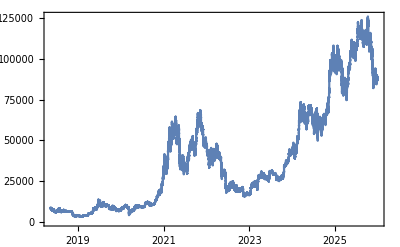

```mathematica
DateListPlot[hourlyPrices,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
Export[base<>"csv/Bitcoin_price-hourly-"<>StringDelete[firstPriceDate, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv",hourlyPrices]
```

/Users/mauro/Projects/Bitcoin/csv/Bitcoin_price-hourly-20251123-20251226.csv

```mathematica
(* Convert to market capitalization, using circulating supply data, from blockchain.info *)
(* Load circulating supply data: https://www.blockchain.com/charts/total-bitcoins *)
supplyJsonData = Import["https://api.blockchain.info/charts/total-bitcoins?timespan=all&sampled=true&metadata=false&daysAverageString=1d&cors=true&format=json"];
```

```mathematica
supplyJson=supplyJsonData[[6]][[2]]
```

```mathematica
supplyTs=supplyJson[[All, 1]][[All,2]];
supplyQuantity=supplyJson[[All, 2]][[All,2]];
```

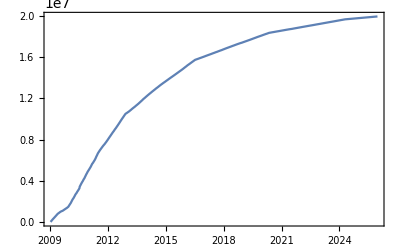

```mathematica
supplyTimestamps=MapThread[{#1, #2}&,{supplyTs, supplyQuantity}];
DateListPlot[supplyTimestamps,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Create an interpolating function from it *)
supplyFunction=Block[{},Off[ InterpolatingFunction::dmval];Interpolation[supplyTimestamps]]
```

InterpolatingFunction[…]

```mathematica
{supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}
```

{1231568277,1766354262}

```mathematica
{hourlyPrices[[1]][[1]],hourlyPrices[[-1]][[1]]}
```

{1526364000,1766793600}

```mathematica
{supplyFunction[hourlyPrices[[1]][[1]]], supplyFunction[hourlyPrices[[-3]][[1]]]}
```

{1.70344×10^7,1.99675×10^7}

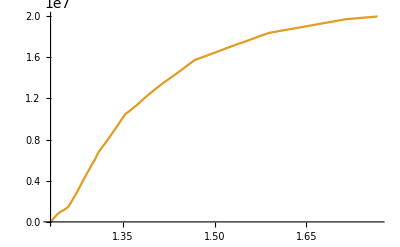

```mathematica
Plot[{,supplyFunction[i]}, {i, supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}]
```

```mathematica
(* Generate hourly market capitalization data *)
hourlyMarketCap={#[[1]], #[[2]]*supplyFunction[#[[1]]]}&/@hourlyPrices
```

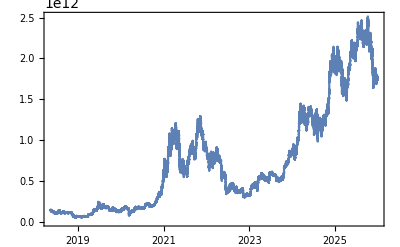

```mathematica
DateListPlot[hourlyMarketCap, DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Use the Log Market Cap *)
logMarketCap= {#[[1]], Log[#[[2]]]}&/@hourlyMarketCap
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2026 bubble turning point: *)
(* Generalized to multiple bubbles *)
bubblesDate={{"2025-11-23", lastPriceDate}}
```

{{2025-11-23,2025-12-26}}

```mathematica
bubbleN=Length[bubblesDate]
```

1

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1763852400,1766703600}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{33}

```mathematica
bubbles=Table[Select[logMarketCap,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, bubbleN}];
#[[1]]&/@bubbles
```

{{1763852400,28.1555}}

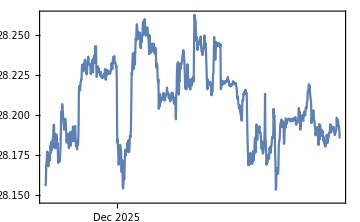

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{1.97506,0.293429}}

```mathematica
Length/@bubblesScaled
```

{793}

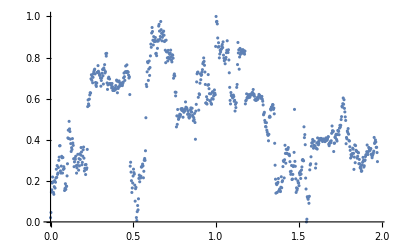

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
ListPlot[bubblesScaled]
```

```mathematica
(* Export bubbles data: *)
bubbleScaledCsvs=MapIndexed[Export[base<>"csv/bubbleScaled-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,bubblesScaled]
```

{/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-1.tsv}

```mathematica
(* Our "goodness of fit" control parameter. The smaller the better. i.e. stricter hypothesis testing will be. *)
(* Empirically, spans greater than 0.1 indicate that our prediction is not very reliable / trustworthy. *)bestSpan=0.1
```

0.1

```mathematica
(* Get params from R: *)
rInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@bubbleScaledCsvs;
```

```mathematica
rRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@rInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
rParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@rRuns
```

{{15.9681,771.991}}

```mathematica
(* {RSS, SE, SE of the fit}: *)
rErrors=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-6;;;;2]]&/@rRuns
```

{{6.61056,0.0925928,0.0125493}}

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
bestFits = LoessR[#, Scaled[bestSpan], #[[All, 1]], {InterpolationOrder-> 1}]&/@bubblesScaled;
```

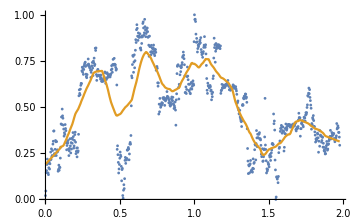

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, Scaled[bestSpan], t ]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, bubbleN}];
```

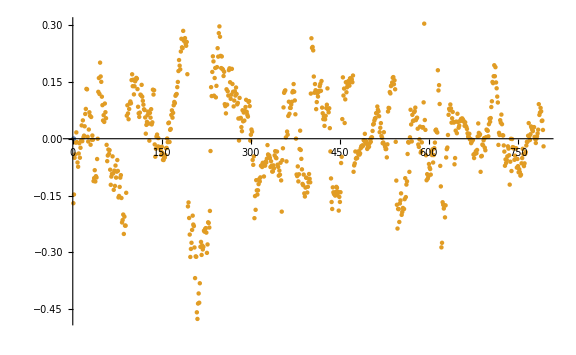

```mathematica
(* Plot residuals: *)
ListPlot[{{0,0},#}, ImageSize->Large]&/@ℛs
```

```mathematica
(* Standard deviations: *)
stdDevℛs=StandardDeviation /@ℛs
```

{0.120564}

```mathematica
(* Standardized residuals: *)
stdℛs = MapThread[#1/#2&,{ℛs, stdDevℛs}];
```

```mathematica
(* RSS: *)
ℛsSS =Total[#^2]&/@ℛs
```

{11.513}

```mathematica
(* Larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[1]]]&,{ℛsSS,rErrors}]
```

{11.513 > 6.61056}

```mathematica
(* Residual Standard Error(s): *)
ℛsSEs=MapThread[√(Total[#1^2]/(Length[#1]-#2[[1]]))&,{ℛs,rParams}]
```

{0.121724}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.121724 > 0.0925928}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(Length[#1]-#2[[1]]))&,{ℛs,rParams, rErrors}]
```

{0.0922359}

```mathematica
ℛsSEs=MapThread[√(Total[#1^2]/(#2[[2]]))&,{ℛs,rParams}]
```

{0.122121}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.122121 > 0.0925928}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(#2[[2]]))&,{ℛs,rParams, rErrors}]
```

{0.0925365}

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
numParams=7;
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Select first bubble for fitting: *)
bubble=1
```

1

```mathematica
(* Or, select last bubble for fitting: *)
bubble=bubbleN
```

```mathematica
(* Use the selected bubble: *)
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* Use the params for the selected bubble: *)
{estimatedNParams, effectiveDfs}=rParams[[bubble]]
```

{15.9681,771.991}

```mathematica
(* Profiling over 0.1 < m < 1, 3 < ω < 14 and 1. < tc < 2 months in the future *)
minM=0.1;
maxM=1;
minω=3;
maxω=14;
months=2;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define `months` in the future scaled interval endpoint: *)
bubbleScaled[[-1]][[1]]
maxTc=bubbleScaled[[-1]][[1]]+(bubblesDays[[bubble]]+30 months)/bubblesDays[[bubble]]//N
```

1.97506

4.79324

```mathematica
(* Define 3 days resolution scaled interval step: *)
stepTc=3/bubblesDays[[bubble]]//N
```

0.0909091

```mathematica
(* Define 5 days resolution scaled initial time step *)
stepTi=5/bubblesDays[[bubble]]//N
```

0.151515

```mathematica
(* Slow. Shortcut below *)
fits=Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[ParallelTable[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
RSS=Total[ℛ^2],
RSS/(Length[ℛ]-numParams),
StandardDeviation[ℛ],
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10}, {ω,minω,maxω,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], RSS-> bestFit[[6]],ℛerror-> bestFit[[7]], ℛσ-> bestFit[[8]],LL-> bestFit[[9]]},bestFit[[5]]], {t1, Range[0,1/2+stepTi, stepTi]}]//AbsoluteTiming
```

{692.738,{{a→14.2981,b→-4.53991,c→0.358982,d→-1.56187,T_1→0.,tc→4.70244,m→1.,ω→3.,RSS→22.5231,ℛerror→0.0286553,ℛσ→0.168636,LL→1342.48,ρ→0.963992,σ→-0.0448171,μ→-3.35772×10^-16},{a→0.190679,b→0.369999,c→0.164744,d→-0.0280783,T_1→0.151515,tc→1.97516,m→0.5,ω→4.4,RSS→19.5312,ℛerror→0.0269395,ℛσ→0.163458,LL→1241.57,ρ→0.961678,σ→-0.0447862,μ→9.31701×10^-18},{a→0.186783,b→0.366867,c→0.129875,d→0.0559503,T_1→0.30303,tc→2.15698,m→1.,ω→6.9,RSS→16.4517,ℛerror→0.0247766,ℛσ→0.156699,LL→1135.84,ρ→0.958867,σ→-0.0444468,μ→-1.10695×10^-17},{a→-0.130787,b→0.332665,c→-0.0438104,d→-0.0682448,T_1→0.454545,tc→3.15698,m→1.,ω→13.9,RSS→15.7176,ℛerror→0.0260656,ℛσ→0.160651,LL→1017.05,ρ→0.957815,σ→-0.046131,μ→4.35333×10^-18},{a→-0.0775925,b→0.470165,c→0.0291052,d→-0.0884636,T_1→0.606061,tc→2.61153,m→1.,ω→14.,RSS→7.91403,ℛerror→0.0146015,ℛσ→0.120173,LL→960.621,ρ→0.936728,σ→-0.0420292,μ→-1.84827×10^-17}}}

```mathematica
(* Shortcut: *)
fits=;
```

```mathematica
(* Timing in minutes: *)
fits[[1]]/60
```

11.5456

```mathematica
fits=fits[[2]];
```

```mathematica
fits[[All,{5,6,11,12}]]//TableForm
```

T_1→0. | tc→4.70244 | ℛσ→0.168636 | LL→1342.48
T_1→0.151515 | tc→1.97516 | ℛσ→0.163458 | LL→1241.57
T_1→0.30303 | tc→2.15698 | ℛσ→0.156699 | LL→1135.84
T_1→0.454545 | tc→3.15698 | ℛσ→0.160651 | LL→1017.05
T_1→0.606061 | tc→2.61153 | ℛσ→0.120173 | LL→960.621

```mathematica
(* Average tc: *)
meanTc=Total[fits[[All,6]][[All,2]]]/Length[fits]
```

2.92062

```mathematica
minTc=Min[fits[[All,6]][[All,2]]]
maxTc=Max[fits[[All,6]][[All,2]]]
```

1.97516

4.70244

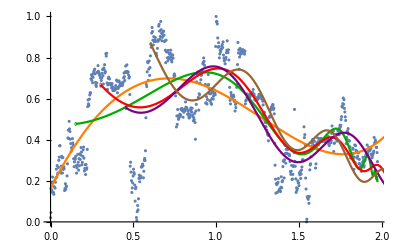

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black, Lighter[Gray], Lighter[Green], Lighter[Red], Lighter[Purple], Lighter[Brown], Lighter[Blue],Lighter[Orange]};
circles=Table[{colors[[Mod[i, Length[colors]]+1]],Thickness[0.0012],Circle[{i stepTi,lpplsModel/.fits[[i+1]]/.ti-> i stepTi},{0.005,0.0085}]}, {i, 0,Length[fits]-1}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>i stepTi,Evaluate[lpplsModel/.fits[[i+1]]],""], {i,0,Length[fits]-1}], {ti, 0, maxTc}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* 4. Rejection criteria: See if the residuals errors of the fits (ℛerror field) are below the 95% of the simulated (standardized) RSSs: *)
T1s=Subscript[T, 1]/.fits
ℛerrors=ℛerror/.fits
RSSs=RSS/.fits
ℛσs=ℛσ/.fits
```

{0.,0.151515,0.30303,0.454545,0.606061}

{0.0286553,0.0269395,0.0247766,0.0260656,0.0146015}

{22.5231,19.5312,16.4517,15.7176,7.91403}

{0.168636,0.163458,0.156699,0.160651,0.120173}

```mathematica
Export[base<>"csv/t1s.tsv", Join[{{"t1"}},T1s]]
```

/Users/mauro/Projects/Bitcoin/csv/t1s.tsv

```mathematica
(* Only last bubble *)
npBestFit=bestFits[[bubble]];
```

```mathematica
nPℓ=Length[npBestFit];
nPℓ
```

793

```mathematica
(* Plot of the residuals of the non-parametric fit vs the residuals of the parametric fit: *)
(* Non-parametric residuals: *)
npℛs=ℛs[[bubble]];
```

```mathematica
(* Parametric residuals: *)
fullFit[t_]:=lpplsModel/.fits[[1]]/.ti-> t
pℛs=Table[bubbleScaled[[i]][[2]]-fullFit[bubbleScaled[[i]][[1]]],{i,1,Length[bubbleScaled]}];
```

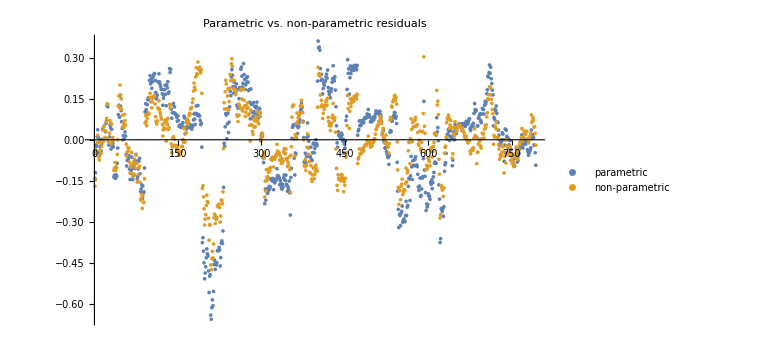

```mathematica
ListPlot[{pℛs,npℛs}, ImageSize->Large, {PlotLabel-> "Parametric vs. non-parametric residuals", PlotLegends->{"parametric","non-parametric"}}]
```

```mathematica
(* RSSs: *)
Total[#^2]&/@{npℛs, pℛs}
```

{11.513,22.5231}

```mathematica
(* Residual Standard Errors: *)
{√(Total[npℛs^2]/effectiveDfs),√(Total[pℛs^2]/(Length[pℛs]-numParams)) }
```

{0.122121,0.169279}

```mathematica
(* Mean residual squared error: *)
{Total[npℛs^2]/effectiveDfs,Total[pℛs^2]/(Length[pℛs]-numParams) }
```

{0.0149134,0.0286553}

```mathematica
selN=Length[T1s];
selN
```

5

```mathematica
selNpBestFit=Table[npBestFit[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selNpBestFit
```

{793,673,553,433,313}

```mathematica
selBubbleScaled2=Table[bubbleScaled[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selBubbleScaled2
```

{793,673,553,433,313}

```mathematica
(* Export selected bubbles: *)
selBubbleScaledCsvs=MapIndexed[Export[base<>"csv/selBubbleScaled-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,selBubbleScaled2];
```

```mathematica
selBubbleScaled=#[[All,2]]&/@selBubbleScaled2;
```

```mathematica
selNpℛs=Table[selBubbleScaled[[i]]-selNpBestFit[[i]], {i, 1,selN}];
```

```mathematica
(* Structural checks: *)
Length/@selNpℛs
```

{793,673,553,433,313}

```mathematica
selBubbleScaled[[1]][[1]]==bubbleScaled[[1]][[2]]
selNpBestFit[[1]][[1]]==npBestFit[[1]]
selNpℛs[[1]][[1]]==ℛs[[bubble]][[1]]
```

True

True

True

```mathematica
(* Magnitude of the parametric residual fits: *)
ℛerrors
```

{0.0286553,0.0269395,0.0247766,0.0260656,0.0146015}

```mathematica
RSSs
```

{22.5231,19.5312,16.4517,15.7176,7.91403}

```mathematica
(* For each selection, do the simulations, and compute all the statistics: *)
(* Standard deviations: *)
selStdDevℛs=StandardDeviation[#]& /@selNpℛs
```

{0.120564,0.122698,0.0989653,0.0941313,0.0821291}

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
selEstimatedAR1Models=FindProcessParameters[#,ar1Process]&/@selNpℛs
```

{{ρ→0.929836,σ→-0.0443365,μ→0.0000684915},{ρ→0.932925,σ→-0.044147,μ→0.0000594258},{ρ→0.906188,σ→-0.041812,μ→0.000795184},{ρ→0.896756,σ→-0.0416074,μ→0.000329508},{ρ→0.87928,σ→-0.0390559,μ→-0.000337947}}

```mathematica
(* Compute the log-likelihood of the fit *)
selEstimatedProcesses=ar1Process/.#&/@selEstimatedAR1Models
logLikelihoods=Table[LogLikelihood[selEstimatedProcesses[[i]],selNpℛs[[i]]], {i, Length[T1s]}]
```

{ARProcess[0.0000684915,{0.929836},0.00196572],ARProcess[0.0000594258,{0.932925},0.00194896],ARProcess[0.000795184,{0.906188},0.00174825],ARProcess[0.000329508,{0.896756},0.00173118],ARProcess[-0.000337947,{0.87928},0.00152536]}

{1351.28,1145.3,972.582,761.682,570.551}

```mathematica
(* Step 2: Characterize error variance. *)
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
(* Allowing for the distribution of the residual standard error on different window sizes to be approximated by Monte Carlo. *)
selNPointss=Length/@selNpℛs;
nSims=1000;
selSims=ParallelTable[RandomFunction[selEstimatedProcesses[[i]],{0,selNPointss[[i]]-1},nSims], {i,selN}];
selNpℛsPlots=ParallelTable[MapThread[{#1,#2}&,{Range[0,selNPointss[[i]]-1],selNpℛs[[i]][[;;selNPointss[[i]]]]}], {i,selN}];
selPaths=#["Paths"]&/@selSims;
```

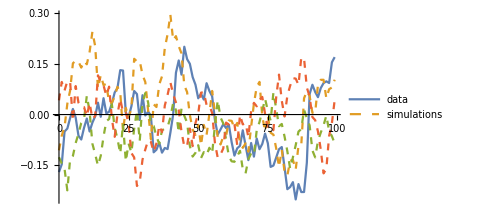
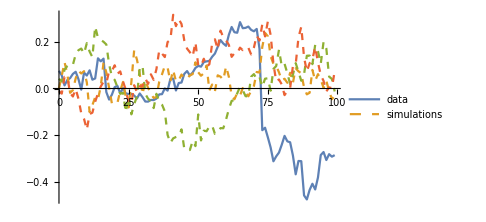
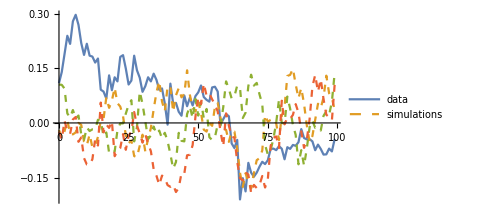
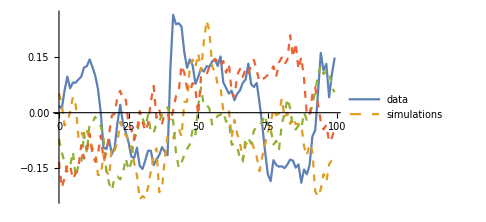
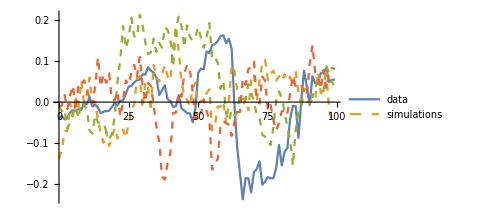

```mathematica
(* Show some simulations and data points *)
showSims=3;
showPoints=100;
Table[ListLinePlot[Join[{selNpℛsPlots[[i]][[;;showPoints]]}, selPaths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,selN}]
```

```mathematica
(* The estimated number of parameters of the sample selections fits: *)
(* From R's loess, using list of (selections) effective dfs: *)
selRInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@selBubbleScaledCsvs;
```

```mathematica
selRRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@selRInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
selRParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@selRRuns
```

{{15.9681,771.991},{16.0193,651.929},{16.0882,531.844},{16.1982,411.707},{16.3869,291.469}}

```mathematica
effectiveDfs
estimatedNParams
(*selEstimatedDfs=Table[Length[selBubbleScaled[[i]]]-estimatedNParams, {i, selN}]*)
selEffectiveDfs=Table[selRParams[[i]][[2]], {i, selN}]
```

771.991

15.9681

{771.991,651.929,531.844,411.707,291.469}

```mathematica
(* The "mean" RSSs (RSS/df) of the simulations: *)
selMeanRSSs=Table[Map[Total[(#[[All,2]])^2]/selEffectiveDfs[[i]]&,selPaths[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selMeanRSSs*)
```

```mathematica
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^3.," GB"}];
Needs["Utilities`CleanSlate`"]
memory
```

Memory Used: 0.561345 GB

```mathematica
Remove[selSims]
Remove[selNpℛsPlots]
memory
```

Memory Used: 0.561437 GB

```mathematica
CleanSlate[];
memory
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 46479 Kb

Memory Used: 0.517232 GB

```mathematica
(* The standardized "mean" RSSs: *)
selStdMeanRSSs=Table[Map[#/selStdDevℛs[[i]]&,selMeanRSSs[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selStdMeanRSSs*)
```

```mathematica
(* Count *)
selCounts=Table[With[{ℛerror= ℛerrors[[i]]},Select[selMeanRSSs[[i]],#>ℛerror &]//Length],{i,selN}]
```

{0,0,0,0,1}

```mathematica
selPValues=Table[selCounts[[i]]/Length[selMeanRSSs[[i]]], {i, selN}]//N
```

{0.,0.,0.,0.,0.001}

```mathematica
selRejected=#<(1-0.95)&/@selPValues
```

{True,True,True,True,True}

```mathematica
(* Take the first / largest that is not rejected *)
firstNotRejectedIndex=Select[Table[{i,selRejected[[i]]==False},{i,selN}], #[[2]]&]//First//#[[1]]&
```

First::nofirst: {} has zero length and no first element.

{}

```mathematica
(* Take the one with the min tc *)
minTc=Min[fits[[;;,6,2]]]
```

1.97516

```mathematica
minTcIndex=Select[Table[{i,fits[[i,6,2]]==minTc},{i,selN}],#[[2]]&]//First//#[[1]]&
```

2

```mathematica
index=If[NumericQ[firstNotRejectedIndex], firstNotRejectedIndex,minTcIndex]
```

2

```mathematica
selFit={fits[[index]], "index"-> index}//Flatten
```

{a→0.190679,b→0.369999,c→0.164744,d→-0.0280783,T_1→0.151515,tc→1.97516,m→0.5,ω→4.4,RSS→19.5312,ℛerror→0.0269395,ℛσ→0.163458,LL→1241.57,ρ→0.961678,σ→-0.0447862,μ→9.31701×10^-18,index→2}

```mathematica
bestIndex=index
fit=fits[[bestIndex]]
```

2

{a→0.190679,b→0.369999,c→0.164744,d→-0.0280783,T_1→0.151515,tc→1.97516,m→0.5,ω→4.4,RSS→19.5312,ℛerror→0.0269395,ℛσ→0.163458,LL→1241.57,ρ→0.961678,σ→-0.0447862,μ→9.31701×10^-18}

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* Do it over the best params *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

0.5

4.4

1.97516

1241.57

```mathematica
t1=Subscript[T, 1]/.fit
```

0.151515

```mathematica
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&];
```

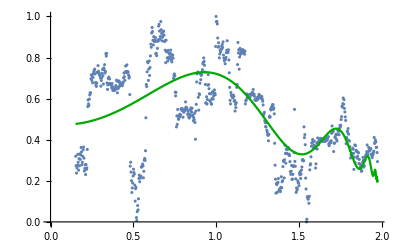

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{colors[[bestIndex]]}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→0.190679,b→0.369999,c→0.164744,d→-0.0280783,T_1→0.151515,tc→1.97516,m→0.5,ω→4.4,RSS→19.5312,ℛerror→0.0269395,ℛσ→0.163458,LL→1241.57,ρ→0.961678,σ→-0.0447862,μ→9.31701×10^-18}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest];
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.961678,σ→-0.0447862,μ→9.31701×10^-18}

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match. *)
```

```mathematica
(* Now sligthly vary tc, and recompute residuals until the LL is 1.92 times below the max: *)
lowCItc=bestTc;
lowCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/1000;
oldSign=1;
Monitor[While[delta=bestLL-lowCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
lowCItc=lowCItc+ precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest];
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],{delta}]
delta
{lowCItc, bestTc}
```

LessEqual::nord: Invalid comparison with -1.85186×10^8+1.57934×10^9 ⅈ attempted.

Less::nord: Invalid comparison with -1.85186×10^8+1.57934×10^9 ⅈ attempted.

LessEqual::nord: Invalid comparison with -1.85186×10^8+1.57934×10^9 ⅈ attempted.

Less::nord: Invalid comparison with -1.85186×10^8+1.57934×10^9 ⅈ attempted.

-1.85186×10^8+1.57934×10^9 ⅈ

{1.97416,1.97516}

```mathematica
(* Let's do the upper leg of the CI: *)
highCItc=bestTc;
highCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/100;
oldSign=-1;
Monitor[While[delta=bestLL-highCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
highCItc=highCItc- precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest];
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],delta]
delta
{lowCItc, bestTc, highCItc}
```

1.92006

{1.97416,1.97516,2.05329}

```mathematica
(* Dates correction: *)
lastScaledTc=bubbleBest[[-1]][[1]]
```

1.97506

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc/lastScaledTc]
```

Thu 25 Dec 2025 23:38:20

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc/lastScaledTc]
```

Fri 26 Dec 2025 00:02:24

```mathematica
(* And the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc/lastScaledTc]
```

Sat 27 Dec 2025 07:22:05

```mathematica
(* With the mean tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc/lastScaledTc]
```

Sat 10 Jan 2026 19:10:02

```mathematica
(* With the max tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] maxTc/lastScaledTc]
```

Mon 9 Feb 2026 13:40:35

```mathematica
(* With the min tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] minTc/lastScaledTc]
```

Fri 26 Dec 2025 00:02:24

```mathematica
(* For reference: *)
{#[[5]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[5]][[2]]/lastScaledTc],#[[6]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[6]][[2]]/lastScaledTc]}&/@fits//TableForm
```

T_1→0. | Sun 23 Nov 2025 00:00:00 | tc→4.70244 | Mon 9 Feb 2026 13:40:35
T_1→0.151515 | Tue 25 Nov 2025 12:45:27 | tc→1.97516 | Fri 26 Dec 2025 00:02:24
T_1→0.30303 | Fri 28 Nov 2025 01:30:54 | tc→2.15698 | Mon 29 Dec 2025 00:56:57
T_1→0.454545 | Sun 30 Nov 2025 14:16:21 | tc→3.15698 | Wed 14 Jan 2026 17:56:57
T_1→0.606061 | Wed 3 Dec 2025 03:01:49 | tc→2.61153 | Mon 5 Jan 2026 15:13:18

```mathematica
(* Compute market cap at the low leg of the best Tc: *)
bestM=bestLppls[bestTc-epsilon,bestTc]
```

0.1929

```mathematica
lowCIM=bestLppls[lowCItc,bestTc]
```

0.204341

```mathematica
lastScaledM=bubbleBest[[-1]][[2]]
```

0.293429

```mathematica
lastPriceDate
```

2025-12-26

```mathematica
(* Closing market cap at lastPriceDate date (`$lastPriceDate`) (https://coinmarketcap.com/currencies/bitcoin/historical-data/https://coinmarketcap.com/currencies/bitcoin/historical-data/Nonehttps://coinmarketcap.com/currencies/bitcoin/historical-data/HyperlinkActionRecycledHyperlinkActive) (Millions of USD): *)
(* Automated download *)
timeStartTs=UnixTime[lastPriceDate];
timeEndTs=timeStartTs+86400;
latestMarketCapUrl="https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart="<>ToString[timeStartTs]<>"&timeEnd="<>ToString[timeEndTs]<>"&interval=1d"
```

https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart=1766703600&timeEnd=1766790000&interval=1d

```mathematica
latestMarketCapData=Import[latestMarketCapUrl]
```

```mathematica
latestMarketCap=Flatten[latestMarketCapData[[1]][[2]][[5]][[2]]][[5]][[2]][[7]][[2]]/10^7
```

195895.443212685

```mathematica
(* Plot predicted market cap evolution (USD) :*)
fixDate[brokenDate_]:= StringTake[brokenDate,2]<>"/"<>StringTake[brokenDate,3;;]
ticksH[min_,max_]:=Table[{i,Rotate[fixDate[Block[{$DateStringFormat={"Day","Month","/","YearShort"}},DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]i/lastScaledTc]]], π/3]},{i,{t1,lastScaledTc,lowCItc, bestTc, highCItc}}]
```

```mathematica
ticksVM[min_,max_]:=Table[{i,"$ "<>ToString[IntegerPart[i latestMarketCap/Exp[lastScaledM]]]<>"M"},{i,min, max,1}]
```

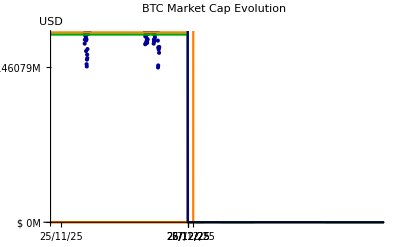

```mathematica
marketCapPrediction=Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Market Cap Evolution",PlotRange->{{0,maxTc},{0,Exp[bestM]}}, Ticks->{ticksH,ticksVM},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[Exp[lpplsModel/.fit]],UnitStep[ti-lowCItc]Exp[bestM+1],UnitStep[ti-highCItc]Exp[bestM+1]/.fit, UnitStep[lowCItc-ti]Exp[lowCIM],UnitStep[bestTc-ti]Exp[bestM],UnitStep[lastScaledTc-ti]Exp[lastScaledM]}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/BTC_MarketCapPrediction-"<>lastPriceDate<>".png",marketCapPrediction]
```

/Users/mauro/Projects/Bitcoin/png/BTC_MarketCapPrediction-2025-12-26.png

```mathematica
mToMarketCap[m_]:= latestMarketCap/Exp[lastScaledM] Exp[m]
```

```mathematica
lowCIMarketCap=mToMarketCap[lowCIM]
```

179198.

```mathematica
bestMarketCap=mToMarketCap[bestM]
```

177160.

```mathematica
(* The price is the ratio of the market cap (in Millions USD) to the (predicted) supply at the date: *)
mToPrice[m_, date_]:=mToMarketCap[m]10^7/supplyFunction[UnixTime[date]]
```

```mathematica
tcToDate[tc_]:= DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]tc/lastScaledTc]
```

```mathematica
(* Check: *)
lastPrice=mToPrice[lastScaledM,tcToDate[lastScaledTc]]
```

98109.2

```mathematica
lowCIPrice=mToPrice[lowCIM, tcToDate[lowCItc]]
```

89746.9

```mathematica
bestPrice=mToPrice[bestM, tcToDate[bestTc]]
```

88726.

```mathematica
(* Plot predicted price evolution (USD) :*)
ticksVPrice[min_,max_]:=Table[{i,"$"<>ToString[IntegerPart[i]]},{i,min, max,50000}]
```

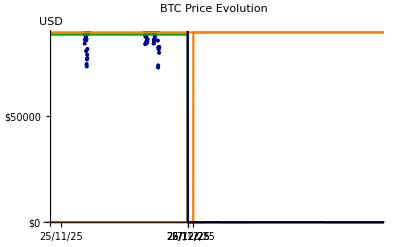

```mathematica
pricePrediction=Show[ListPlot[{#[[1]], mToPrice[#[[2]], tcToDate[#[[1]]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Price Evolution",PlotRange->{{0,maxTc},{0,bestPrice}}, Ticks->{ticksH,ticksVPrice},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[mToPrice[lpplsModel/.fit, tcToDate[ti]]],UnitStep[ti-lowCItc](bestPrice+1000),UnitStep[ti-highCItc](bestPrice+1000)/.fit, UnitStep[lowCItc-ti]lowCIPrice,UnitStep[bestTc-ti]bestPrice,UnitStep[lastScaledTc-ti]lastPrice}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/BTC_PricePrediction-"<>lastPriceDate<>".png",pricePrediction]
```

/Users/mauro/Projects/Bitcoin/png/BTC_PricePrediction-2025-12-26.png